```mathematica
x[t_]:=0+Cos[2π *3*t]
```

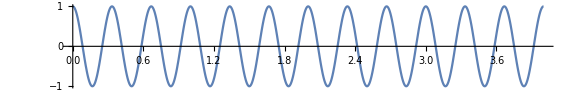

```mathematica
Plot[x[t],{t,0,4},AspectRatio->1/6,ImageSize->Large]
```

```mathematica
FourierTransform[x[t],t,ω,FourierParameters->{0, -2*Pi}]
```

1/2 DiracDelta[-3+ω]+1/2 DiracDelta[3+ω]

```mathematica
s=FourierSeries[SquareWave[t/2],t,14,FourierParameters->{1, -Pi}]//ExpToTrig
```

(4 Sin[π t])/π+(4 Sin[3 π t])/(3 π)+(4 Sin[5 π t])/(5 π)+(4 Sin[7 π t])/(7 π)+(4 Sin[9 π t])/(9 π)+(4 Sin[11 π t])/(11 π)+(4 Sin[13 π t])/(13 π)

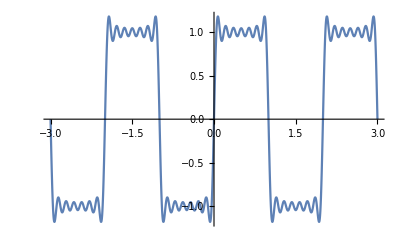

```mathematica
Plot[s,{t,-3,3}]
```

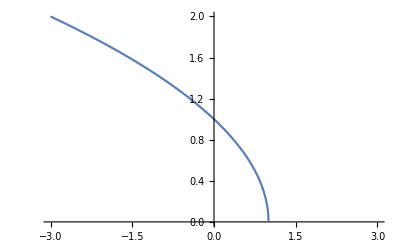

```mathematica
Plot[√(-(t-1)),{t,-3,3}]
```

```mathematica
x[t_]:=Piecewise[{{Mod[t,2],0<=Mod[t,2]<1},{√(-Mod[t,2]+2),1<=Mod[t,2]<2},{Indeterminate,True}}]
```

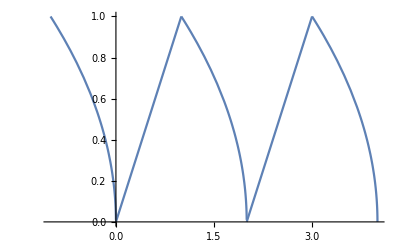

```mathematica
Plot[x[t],{t,-1,4},MaxRecursion->10]
```

```mathematica
FourierSeries[x[t],t,10,FourierParameters->{1, -(2π)/2}]//ExpToTrig//FullSimplify
```

-1/(3175200 π^2)(-1852200 π^2+793800 Cos[π t] (8+π (√2+2 π (ExpIntegralE[-1/2,-ⅈ π]+ExpIntegralE[-1/2,ⅈ π])))+88200 Cos[3 π t] (8+π (√6+18 π (ExpIntegralE[-1/2,-3 ⅈ π]+ExpIntegralE[-1/2,3 ⅈ π])))+99225 π Cos[4 π t] (√2+16 π (ExpIntegralE[-1/2,-4 ⅈ π]+ExpIntegralE[-1/2,4 ⅈ π]))+31752 Cos[5 π t] (8+π (√10+50 π (ExpIntegralE[-1/2,-5 ⅈ π]+ExpIntegralE[-1/2,5 ⅈ π])))+44100 π Cos[6 π t] (√3+36 π (ExpIntegralE[-1/2,-6 ⅈ π]+ExpIntegralE[-1/2,6 ⅈ π]))+16200 Cos[7 π t] (8+π (√14+98 π (ExpIntegralE[-1/2,-7 ⅈ π]+ExpIntegralE[-1/2,7 ⅈ π])))+9800 Cos[9 π t] (8+3 π (√2+54 π (ExpIntegralE[-1/2,-9 ⅈ π]+ExpIntegralE[-1/2,9 ⅈ π])))+793800 π Cos[2 π t] FresnelS[2]+99225 π Cos[8 π t] FresnelS[4]+31752 √5 π Cos[10 π t] FresnelS[2 √5]+1587600 √2 π FresnelC[√2] Sin[π t]+793800 π FresnelC[2] Sin[2 π t]+176400 √6 π FresnelC[√6] Sin[3 π t]+198450 √2 π FresnelC[2 √2] Sin[4 π t]+63504 √10 π FresnelC[√10] Sin[5 π t]+88200 √3 π FresnelC[2 √3] Sin[6 π t]+32400 √14 π FresnelC[√14] Sin[7 π t]+99225 π FresnelC[4] Sin[8 π t]+58800 √2 π FresnelC[3 √2] Sin[9 π t]+31752 √5 π FresnelC[2 √5] Sin[10 π t])

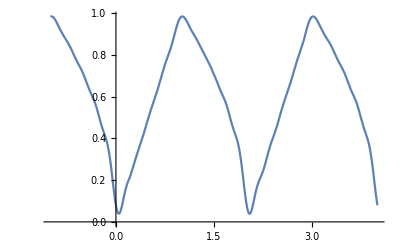

```mathematica
Plot[%67,{t,-1,4}]
```

```mathematica
x[t_]:=Piecewise[{{Mod[t,4],0<=Mod[t,4]<2},{1,2<=Mod[t,4]<3},{-2Mod[t,4]+7,3<=Mod[t,4]<4},{Indeterminate,True}}]
```

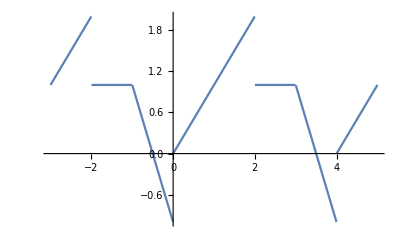

```mathematica
Plot[x[t],{t,-3,5}]
```

```mathematica
s=FourierSeries[x[t],t,30,FourierParameters->{1,-(2π)/4}]
```

3/4-ⅇ^(-ⅈ π t)/π^2-ⅇ^(ⅈ π t)/π^2-ⅇ^(-3 ⅈ π t)/(9 π^2)-ⅇ^(3 ⅈ π t)/(9 π^2)-ⅇ^(-5 ⅈ π t)/(25 π^2)-ⅇ^(5 ⅈ π t)/(25 π^2)-ⅇ^(-7 ⅈ π t)/(49 π^2)-ⅇ^(7 ⅈ π t)/(49 π^2)-ⅇ^(-9 ⅈ π t)/(81 π^2)-ⅇ^(9 ⅈ π t)/(81 π^2)-ⅇ^(-11 ⅈ π t)/(121 π^2)-ⅇ^(11 ⅈ π t)/(121 π^2)-ⅇ^(-13 ⅈ π t)/(169 π^2)-ⅇ^(13 ⅈ π t)/(169 π^2)-ⅇ^(-15 ⅈ π t)/(225 π^2)-ⅇ^(15 ⅈ π t)/(225 π^2)-(ⅇ^((3 ⅈ π t)/2) ((4+2 ⅈ)+3 ⅈ π))/(9 π^2)-(ⅇ^(-5/2 ⅈ π t) ((4+2 ⅈ)-5 ⅈ π))/(25 π^2)-(ⅇ^((5 ⅈ π t)/2) ((4-2 ⅈ)+5 ⅈ π))/(25 π^2)-(ⅇ^((7 ⅈ π t)/2) ((4+2 ⅈ)+7 ⅈ π))/(49 π^2)-(ⅇ^((9 ⅈ π t)/2) ((4-2 ⅈ)+9 ⅈ π))/(81 π^2)-(ⅇ^((11 ⅈ π t)/2) ((4+2 ⅈ)+11 ⅈ π))/(121 π^2)-(ⅇ^((13 ⅈ π t)/2) ((4-2 ⅈ)+13 ⅈ π))/(169 π^2)+(ⅇ^(-15/2 ⅈ π t) ((-4+2 ⅈ)+15 ⅈ π))/(225 π^2)-(ⅇ^((15 ⅈ π t)/2) ((4+2 ⅈ)+15 ⅈ π))/(225 π^2)-(ⅇ^((17 ⅈ π t)/2) ((4-2 ⅈ)+17 ⅈ π))/(289 π^2)-(ⅇ^((19 ⅈ π t)/2) ((4+2 ⅈ)+19 ⅈ π))/(361 π^2)-(ⅇ^((21 ⅈ π t)/2) ((4-2 ⅈ)+21 ⅈ π))/(441 π^2)-(ⅇ^((23 ⅈ π t)/2) ((4+2 ⅈ)+23 ⅈ π))/(529 π^2)-(ⅇ^(-25/2 ⅈ π t) ((4+2 ⅈ)-25 ⅈ π))/(625 π^2)-(ⅇ^((25 ⅈ π t)/2) ((4-2 ⅈ)+25 ⅈ π))/(625 π^2)-(ⅇ^((27 ⅈ π t)/2) ((4+2 ⅈ)+27 ⅈ π))/(729 π^2)-(ⅇ^((29 ⅈ π t)/2) ((4-2 ⅈ)+29 ⅈ π))/(841 π^2)-(ⅈ ⅇ^((ⅈ π t)/2) ((-2-4 ⅈ)+π))/π^2+(ⅈ ⅇ^(-1/2 ⅈ π t) ((-2+4 ⅈ)+π))/π^2+(ⅈ ⅇ^(-3/2 ⅈ π t) ((2+4 ⅈ)+3 π))/(9 π^2)+(ⅈ ⅇ^(-7/2 ⅈ π t) ((2+4 ⅈ)+7 π))/(49 π^2)+(ⅈ ⅇ^(-9/2 ⅈ π t) ((-2+4 ⅈ)+9 π))/(81 π^2)+(ⅈ ⅇ^(-11/2 ⅈ π t) ((2+4 ⅈ)+11 π))/(121 π^2)+(ⅈ ⅇ^(-13/2 ⅈ π t) ((-2+4 ⅈ)+13 π))/(169 π^2)+(ⅈ ⅇ^(-17/2 ⅈ π t) ((-2+4 ⅈ)+17 π))/(289 π^2)+(ⅈ ⅇ^(-19/2 ⅈ π t) ((2+4 ⅈ)+19 π))/(361 π^2)+(ⅈ ⅇ^(-21/2 ⅈ π t) ((-2+4 ⅈ)+21 π))/(441 π^2)+(ⅈ ⅇ^(-23/2 ⅈ π t) ((2+4 ⅈ)+23 π))/(529 π^2)+(ⅈ ⅇ^(-27/2 ⅈ π t) ((2+4 ⅈ)+27 π))/(729 π^2)+(ⅈ ⅇ^(-29/2 ⅈ π t) ((-2+4 ⅈ)+29 π))/(841 π^2)

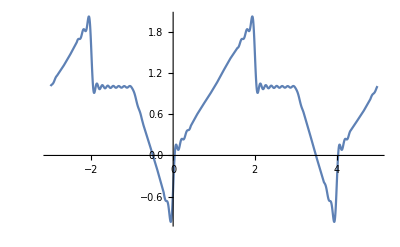

```mathematica
Plot[s,{t,-3,5}]
```

```mathematica
FourierTransform[SquareWave[t],t,ξ,FourierParameters->{0, -2*Pi}]
```

∑_(K[1]=-∞)^∞ 2 DiracDelta[-2 ξ+K[1]] (Piecewise[{{0, K[1]==0}, {-(ⅈ (-1)^K[1] (1+(-1)^K[1]) (-1+ⅈ^K[1])^2)/(2 π K[1]), True}}])

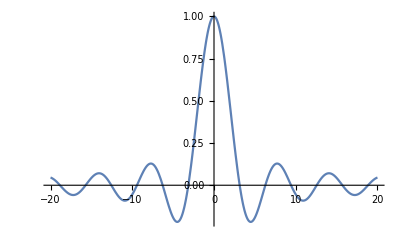

```mathematica
Plot[Sinc[t],{t,-20,20},PlotRange->All]
```

```mathematica
FourierTransform[Sinc[t],t,ξ,FourierParameters->{0, -2*Pi}]
```

1/2 π Sign[1-2 π ξ]+1/2 π Sign[1+2 π ξ]

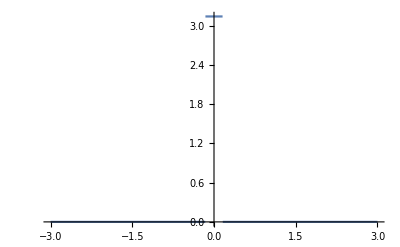

```mathematica
Plot[%,{ξ,-3,3}]
```

```mathematica
Clear[s]
```

```mathematica
p=1/3;
```

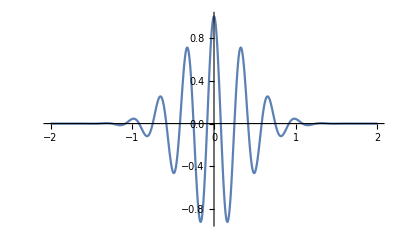

```mathematica
s[t_]:=Cos[(2π/p)t] ⅇ^(-π t^2)
Plot[s[t],{t,-2,2},PlotRange->All]
```

```mathematica
g[t_,ξ_]:=s[t] ⅇ^(-ⅈ(2π ξ)t);
```

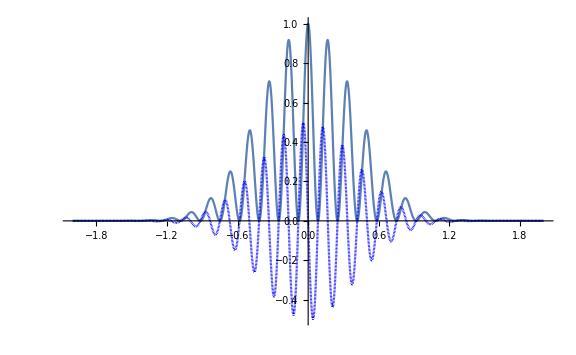

```mathematica
ReImPlot[g[t,3],{t,-2,2},PlotRange->All,ImageSize->Large,ReImStyle->{Automatic,{Blue,Dashing[0]}}]
```

```mathematica
Manipulate[
ReImPlot[g[t,ξ],{t,-2,2},PlotRange->All,ImageSize->Large,ReImStyle->{Automatic,{Blue,Dashing[0]}},
PerformanceGoal->"Quality"],
{ξ,1,5},SaveDefinitions->True
]
```

```mathematica
Integrate[g[t,3],{t,-Infinity,Infinity}]
```

1/2 (1+ⅇ^(-36 π))

```mathematica
%160//N[#,100]&
```

0.5000000000000000000000000000000000000000000000000381435636908616003804349103396680313988639916114905

```mathematica
r=Integrate[g[t,ξ],{t,-Infinity,Infinity}];
ŝ[ξ_]:=Evaluate@r
```

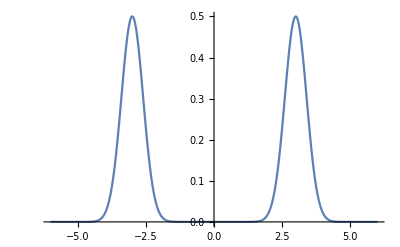

```mathematica
Plot[ŝ[ξ],{ξ,-6,6}]
```

```mathematica
Maximize[{ŝ[ξ],ξ>1},ξ]//N[#,100]&
```

{0.5000000000000000000000000000000000000000000000000381435636908616003804349103396680313988639916118196,{ξ→2.999999999999999999999999999999999999999999999999542277235709660795434781075923983623213632100654251}}

```mathematica
r=FourierTransform[s[t],t,ξ,FourierParameters->{0, -2π}]//TrigToExp//Simplify
```

1/2 (ⅇ^(-π (-3+ξ)^2)+ⅇ^(-π (3+ξ)^2))

```mathematica
ŝ[ξ]==r//FullSimplify
```

True

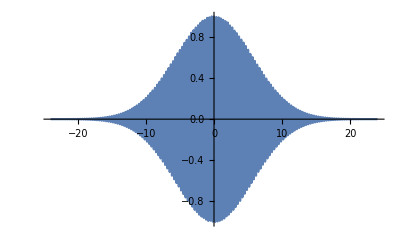

General::munfl: Exp[-50891.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5653.94] is too small to represent as a normalized machine number; precision may be lost.

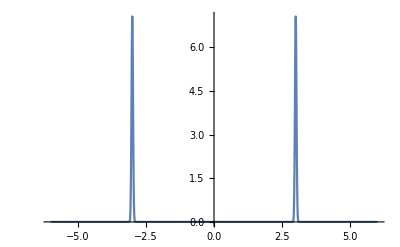

```mathematica
s[t_]:=Cos[(2π/p)t] ⅇ^(-π t^2/200)
Plot[s[t],{t,-24,24},PlotRange->All]
r=FourierTransform[s[t],t,ξ,FourierParameters->{0, -2π}]//TrigToExp//Simplify;
Plot[r,{ξ,-6,6},PlotRange->All]
```

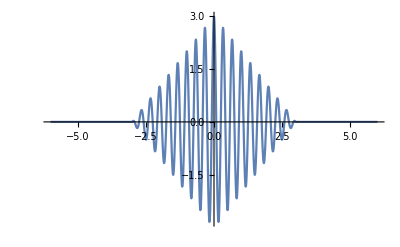

```mathematica
s[t_]:=Cos[(2π/p)t]Max[(-RealAbs[t]+3),0]
Plot[s[t],{t,-6,6},PlotRange->All]
```

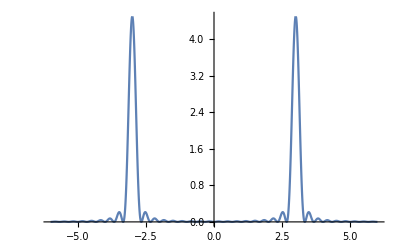

```mathematica
r=FourierTransform[s[t],t,ξ,FourierParameters->{0, -2π}]//TrigToExp//Simplify;
Plot[r,{ξ,-6,6},PlotRange->All]
```

```mathematica
ToExpression["\\frac{1}{\\operatorname{abs}\\left(x\\right)+1}\\cos\\left(2\\pi\\cdot3\\operatorname{abs}\\left(x\\right)\\right)",TeXForm]
```

Cos[2 abs x π·3]/(1+abs x)

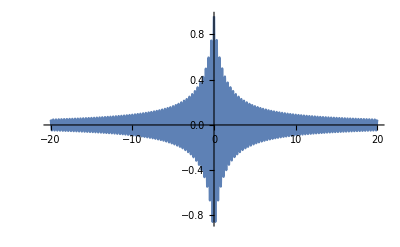

```mathematica
s[t_]:=1/(RealAbs[t]+1)Cos[2π 3RealAbs[t]]
Plot[s[t],{t,-20,20},PlotRange->All]
```

```mathematica
r=FourierTransform[s[t],t,ξ,FourierParameters->{0, -2π}]
Plot[r,{ξ,-6,6},PlotRange->All]
```

-1/2 ⅈ π Cos[2 π ξ]-1/2 Cos[2 π ξ] ExpIntegralEi[-2 ⅈ π (-3+ξ)]-1/2 Cos[2 π ξ] ExpIntegralEi[-2 ⅈ π (3+ξ)]-1/2 ⅈ π Cos[2 π ξ] Floor[1/2-Arg[-3+ξ]/π]-1/2 ⅈ π Cos[2 π ξ] Floor[1/2-Arg[3+ξ]/π]+1/2 π MeijerG[{{0},{1/2}},{{0,0},{1/2}},2 ⅈ π (-3+ξ)]+1/2 π MeijerG[{{0},{1/2}},{{0,0},{1/2}},2 ⅈ π (3+ξ)]-(ⅈ π Cos[2 π ξ])/(4 Sign[-3+ξ])-(ⅈ π Cos[2 π ξ])/(4 Sign[3+ξ])+1/2 π Sin[2 π ξ]-1/2 ⅈ ExpIntegralEi[-2 ⅈ π (-3+ξ)] Sin[2 π ξ]-1/2 ⅈ ExpIntegralEi[-2 ⅈ π (3+ξ)] Sin[2 π ξ]+1/2 π Floor[1/2-Arg[-3+ξ]/π] Sin[2 π ξ]+1/2 π Floor[1/2-Arg[3+ξ]/π] Sin[2 π ξ]+(π Sin[2 π ξ])/(4 Sign[-3+ξ])+(π Sin[2 π ξ])/(4 Sign[3+ξ])

-Graphics-

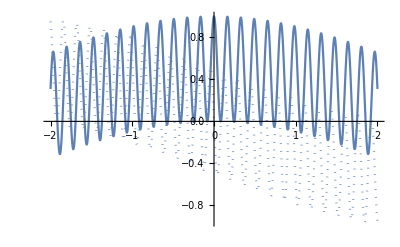

```mathematica
ReImPlot[Cos[2π 3t] ⅇ^(-ⅈ(2π*3.1)t),{t,-2,2}]
```

```mathematica
Clear[p]
```

```mathematica
FourierTransform[Cos[t],t,ξ,FourierParameters->{0, -2*Pi}]
FourierTransform[Sin[t],t,ξ,FourierParameters->{0, -2*Pi}]
FourierTransform[Cos[t+p],t,ξ,FourierParameters->{0, -2*Pi}]
```

π DiracDelta[1-2 π ξ]+π DiracDelta[1+2 π ξ]

-ⅈ π DiracDelta[1-2 π ξ]+ⅈ π DiracDelta[1+2 π ξ]

ⅇ^(ⅈ p) π DiracDelta[1-2 π ξ]+ⅇ^(-ⅈ p) π DiracDelta[1+2 π ξ]

1/2 ⅇ^(-π (-3+ξ)^2)+1/2 ⅇ^(-π (3+ξ)^2)

(0.464888+0.184062 ⅈ) ⅇ^(-π (-3+ξ)^2)+(0.464888-0.184062 ⅈ) ⅇ^(-π (3+ξ)^2)

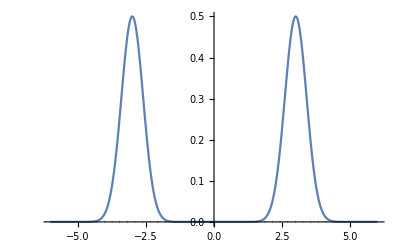

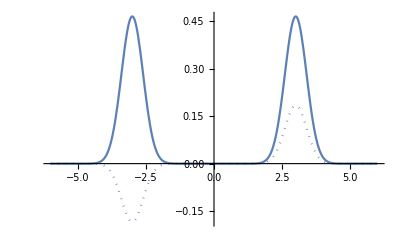

```mathematica
r1=FourierTransform[Cos[2π 3t] ⅇ^(-π t^2),t,ξ,FourierParameters->{0, -2*Pi}]//TrigToExp
r2=FourierTransform[Cos[2π 3(t+0.02)] ⅇ^(-π t^2),t,ξ,FourierParameters->{0, -2*Pi}]//TrigToExp
ReImPlot[r1,{ξ,-6,6},PlotRange->All]
ReImPlot[r2,{ξ,-6,6},PlotRange->All]
```

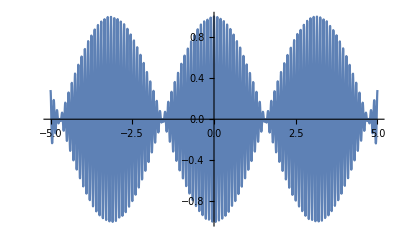

```mathematica
Plot[Cos[t]Cos[2π 10t],{t,-5,5},PlotPoints->30]
```

```mathematica
FourierTransform[(1.2+Cos[t])Cos[2π 10t],t,f,FourierParameters->{0, -2*Pi}]//FullSimplify
```

0.6 DiracDelta[-10+f]+0.6 DiracDelta[10+f]+1.5708 DiracDelta[1+2 (-10+f) π]+1.5708 DiracDelta[1+20 π-2 f π]+1.5708 DiracDelta[1-2 (10+f) π]+1.5708 DiracDelta[1+2 (10+f) π]

```mathematica
InverseFourierTransform[DiracDelta[ξ-f]+DiracDelta[ξ+f]+DiracDelta[0],ξ,t,FourierParameters->{0, -2*Pi}]//ExpToTrig(*//Re//Simplify[#,Assumptions->{t∈Reals}]&*)
```

2 Cos[2 f π t]+DiracDelta[0] DiracDelta[t]

```mathematica
m[t_]:=Sin[2π 2t]
c[t_]:=Cos[2π 20t]
```

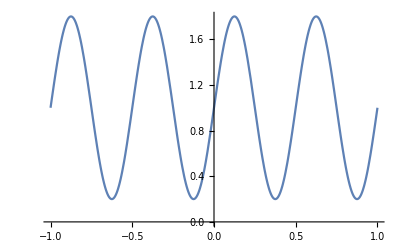

```mathematica
Plot[(m[t]*0.8)/1+1,{t,-1,1}]
```

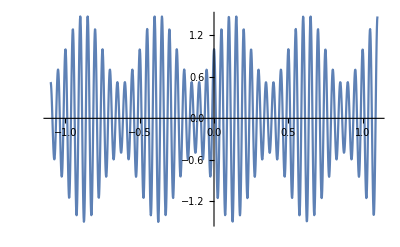

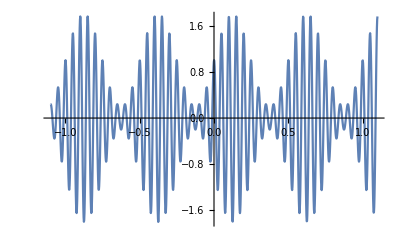

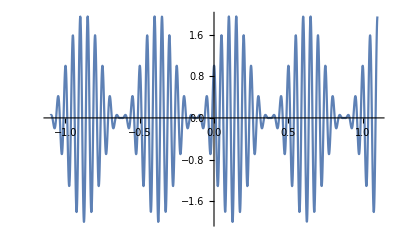

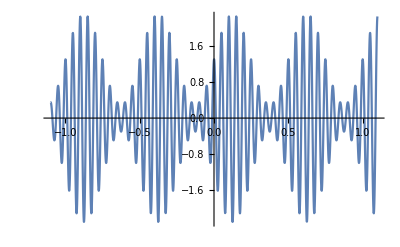

```mathematica
Plot[((m[t]*0.5)/1+1)c[t],{t,-1.1,1.1},PlotPoints->20]
Plot[((m[t]*0.8)/1+1)c[t],{t,-1.1,1.1},PlotPoints->20]
Plot[((m[t]*1)/1+1)c[t],{t,-1.1,1.1},PlotPoints->30]
Plot[((m[t]*1)/1+1.3)c[t],{t,-1.1,1.1},PlotPoints->30]
```

```mathematica
FourierTransform[((m[t]*0.5)/1+1)c[t],t,f,FourierParameters->{0, -2*Pi}]
```

(0.-0.125 ⅈ) DiracDelta[-22+f]+(0.5+0. ⅈ) DiracDelta[-20+f]+(0.+0.125 ⅈ) DiracDelta[-18+f]-(0.+0.125 ⅈ) DiracDelta[18+f]+(0.5+0. ⅈ) DiracDelta[20+f]+(0.+0.125 ⅈ) DiracDelta[22+f]

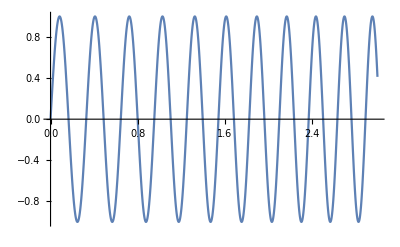

```mathematica
Plot[Sin[2π 3t+t^2],{t,0,3}]
```

```mathematica
Manipulate[
Plot[{iA Cos[2π t],qA Sin[2π t],iA Cos[2π t]+qA Sin[2π t]},{t,-2,2},PlotLegends->{"I","Q","I+Q"},ImageSize->Large,PerformanceGoal->"Quality",PlotRange->{Automatic,{-1.5,1.5}}],
{{iA,1},-1,1},
{{qA,1},-1,1},
SaveDefinitions->True
]
```

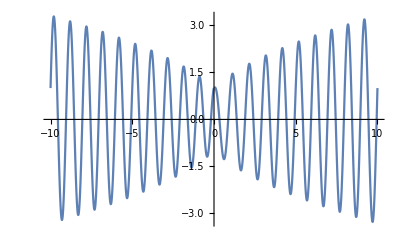

```mathematica
Plot[1 Cos[2π t]+√RealAbs[t] Sin[2π t],{t,-10,10}]
```

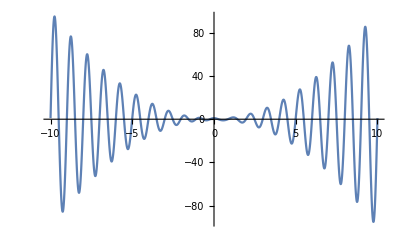

```mathematica
Plot[1 Cos[2π t]+t^2 Sin[2π t],{t,-10,10}]
```

```mathematica
FourierTransform[1 Cos[2π t]+√RealAbs[t] Sin[2π t],t,f,FourierParameters->{0, -2*Pi}]
```

ⅈ/(8 π Abs[-1+f]^(3/2))-ⅈ/(8 π Abs[1+f]^(3/2))+1/2 DiracDelta[-1+f]+1/2 DiracDelta[1+f]

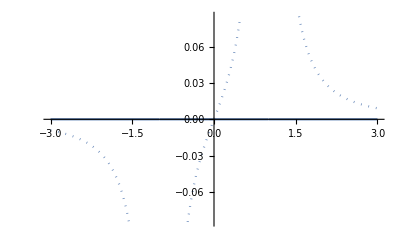

```mathematica
ReImPlot[%108,{f,-3,3}]
```

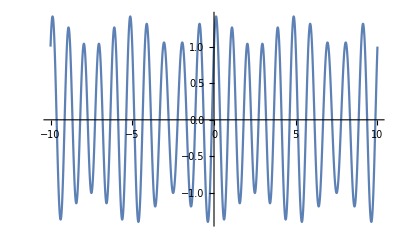

```mathematica
Plot[1 Cos[2π t]+Cos[2π t/10]Sin[2π t],{t,-10,10}]
```

```mathematica
FourierTransform[1 Cos[2π t]+Cos[2π 10t]Sin[2π t],t,f,FourierParameters->{0, -2*Pi}]
```

-1/4 ⅈ DiracDelta[-11+f]+1/4 ⅈ DiracDelta[-9+f]+1/2 DiracDelta[-1+f]+1/2 DiracDelta[1+f]-1/4 ⅈ DiracDelta[9+f]+1/4 ⅈ DiracDelta[11+f]

```mathematica
(*Symmetric spectrum*)
InverseFourierTransform[DiracDelta[f-3]+DiracDelta[f+3],f,t,FourierParameters->{0, -2*Pi}]//ExpToTrig
```

2 Cos[6 π t]

```mathematica
(*Asymmetric!*)
InverseFourierTransform[DiracDelta[f-3]+DiracDelta[f+2],f,t,FourierParameters->{0, -2*Pi}]//ExpToTrig
```

Cos[4 π t]+Cos[6 π t]-ⅈ Sin[4 π t]+ⅈ Sin[6 π t]

```mathematica
Clear["`*"]
```

```mathematica
a[t_]:=(1/2)(Sin[2π 2t] ⅇ^(-π RealAbs[t]/20))+1;
```

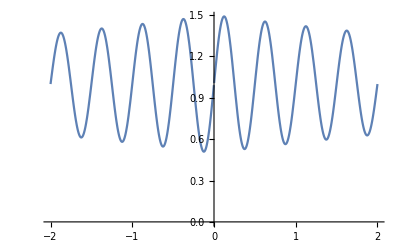

```mathematica
Plot[a[t],{t,-2,2},PlotRange->{Automatic,{0,Automatic}}]
```

```mathematica
m[t_]:=a[t]Cos[2π 20t];
```

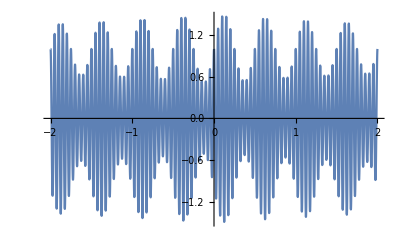

```mathematica
Plot[m[t],{t,-2,2},PlotPoints->100]
```

```mathematica
mCR[t_]:=a[t] ⅇ^(ⅈ(2π 20t));
```

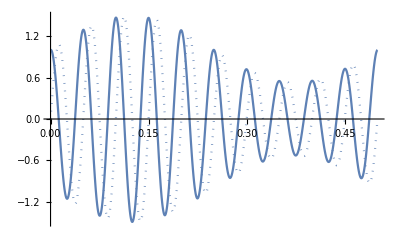

```mathematica
ReImPlot[mCR[t],{t,0,0.5}]
```

```mathematica
ftr=FourierTransform[mCR[t],t,f,FourierParameters->{0, -2*Pi}]
```

-(10 ⅈ)/((774401-70400 f+1600 f^2) π)+(10 ⅈ)/((518401-57600 f+1600 f^2) π)+DiracDelta[-20+f]

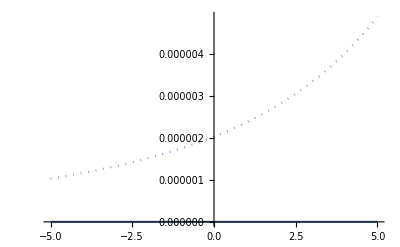

```mathematica
ReImPlot[ftr,{f,-5,5}]
```

```mathematica
FourierTransform[m[t],t,f,FourierParameters->{0, -2*Pi}]
```

-(5 ⅈ)/((-518401+57600 f-1600 f^2) π)-(5 ⅈ)/((774401-70400 f+1600 f^2) π)-(5 ⅈ)/((518401+57600 f+1600 f^2) π)+(5 ⅈ)/((774401+70400 f+1600 f^2) π)+1/2 DiracDelta[-20+f]+1/2 DiracDelta[20+f]

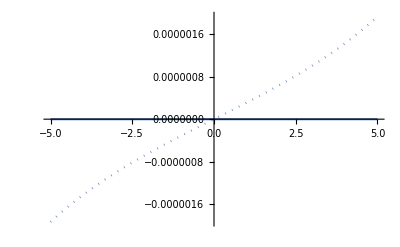

```mathematica
ReImPlot[%182,{f,-5,5}]
```

```mathematica
FullSimplify[ i Cos[t]+q Sin[t]==√(i^2+q^2)Cos[t-ArcTan[q/i]],Assumptions->{{q,t,ϕ}∈Reals,i>=0}]
```

True

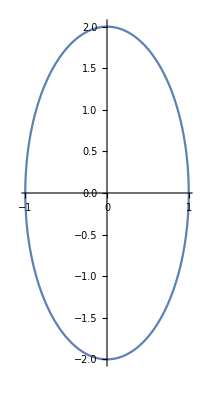

```mathematica
ParametricPlot[{Re[Cos[t]+ⅈ 2Sin[t]],Im[Cos[t]+ⅈ 2 Sin[t]]},{t,0,2π}]
```

```mathematica
(-Cos[t])+ⅈ Sin[t]//TrigToExp
```

-ⅇ^(-ⅈ t)

```mathematica
Cos[t+ϕ[t]]+ⅈ Sin[t]//TrigToExp
```

-1/2 ⅇ^(-ⅈ t)+ⅇ^(ⅈ t)/2+1/2 ⅇ^(-ⅈ t-ⅈ ϕ[t])+1/2 ⅇ^(ⅈ t+ⅈ ϕ[t])

```mathematica
iq[t_]:=Piecewise[{
{{1,1},-2<=t<-1},
{{-1,1},-1<=t<0},
{{-1,-1},0<=t<1},
{{1,-1},1<=t<=2},
{{Indeterminate,Indeterminate},True}
}]
iq[t]
```

Piecewise[{{{1,1}, -2≤t<-1}, {{-1,1}, -1≤t<0}, {{-1,-1}, 0≤t<1}, {{1,-1}, 1≤t≤2}, {{Indeterminate,Indeterminate}, True}}]

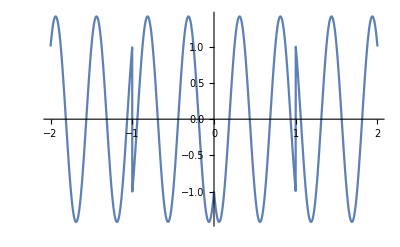

```mathematica
(*QPSK*)
m[t_]:=iq[t][[1]]Cos[2π f t]+iq[t][[2]]Sin[2π f t]/.f->2;
Plot[m[t],{t,-2,2}]
```

```mathematica
iq[t_]:=Piecewise[{
{{1,1},-5<=t<-4},
{{-1,1},-4<=t<-3},
{{-1,-1},-3<=t<-2},
{{1,-1},-2<=t<-1},
{{0,0},-1<=t<0},
{{1,1}/2,0<=t<1},
{{-1,1}/2,1<=t<2},
{{-1,-1}/2,2<=t<3},
{{1,-1}/2,3<=t<=4},
{{Indeterminate,Indeterminate},True}
}]
iq[t]
```

Piecewise[{{{1,1}, -5≤t<-4}, {{-1,1}, -4≤t<-3}, {{-1,-1}, -3≤t<-2}, {{1,-1}, -2≤t<-1}, {{0,0}, -1≤t<0}, {{1/2,1/2}, 0≤t<1}, {{-1/2,1/2}, 1≤t<2}, {{-1/2,-1/2}, 2≤t<3}, {{1/2,-1/2}, 3≤t≤4}, {{Indeterminate,Indeterminate}, True}}]

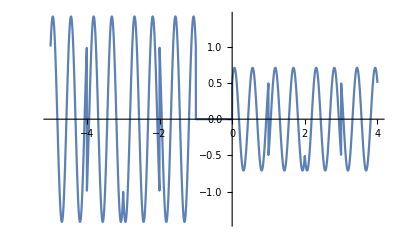

```mathematica
(*9-PSK*)
m[t_]:=iq[t][[1]]Cos[2π f t]+iq[t][[2]]Sin[2π f t]/.f->2;
Plot[m[t],{t,-5,4}]
```

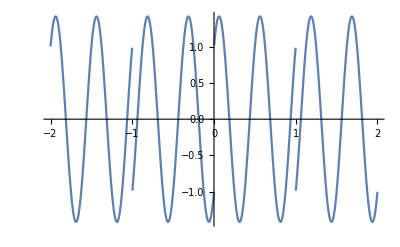

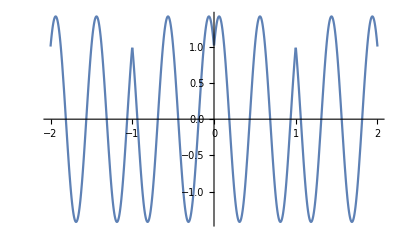

```mathematica
(*BPSK*)
Plot[(*I*)SquareWave[t/2] Cos[2π 2t]+(*Q*)1Sin[2π 2t],{t,-2,2}]
Plot[(*I*)1 Cos[2π 2t]+(*Q*)SquareWave[t/2]Sin[2π 2t],{t,-2,2}]
```

```mathematica
audio=Audio["~/t/square-wave.wav"]
```

```mathematica
Spectrogram[audio]
```

-Graphics-

```mathematica
Manipulate[
Spectrogram[ShortTimeFourier[,ws]],
{ws,1,4096}
]
```

```mathematica
Spectrogram[ShortTimeFourier[,#],PlotLabel->#]&/@{1,5,10,20,30,128,256,512,1024,2048,4096,32768,50000,82355}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
audio=AudioGenerator[Cos[2π((*100+(2000-100)#*)1000#)#]&,1,SampleRate->44100]
```

```mathematica
Spectrogram[audio,1024,SampleRate->44100,PlotRange->{Automatic,{0,3000}}]
```

-Graphics-

```mathematica
chirp=Audio["~/t/chirp.wav"]
```

```mathematica
Spectrogram[chirp,2048,SampleRate->44100,PlotRange->{Automatic,{100,300}}]
```

-Graphics-

```mathematica
(*2.0*PI*(100.0/2.0*t*t+100.0*t)*)
2π(100/2 t^2+100t)//FullSimplify
```

100 π t (2+t)

```mathematica
2π (100+(200-100)*t)t//FullSimplify
```

200 π t (1+t)

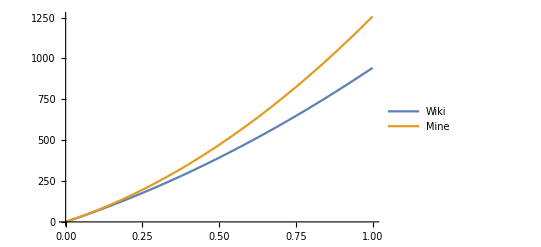

```mathematica
Plot[{%18,%19},{t,0,1},PlotLegends->{"Wiki","Mine"}]
```

```mathematica
-Graphics--Graphics-;
linearChirp[{f0_,f1_},t_]:=Cos[2π((f1-f0)/2 t^2+f0 t)]/;0<=t<=1;
```

```mathematica
audio=AudioGenerator[linearChirp[{1000,2000},#]&,1,SampleRate->44100]
```

```mathematica
Spectrogram[audio,1024,PlotRange->{Automatic,{800,2200}}]
```

-Graphics-

```mathematica
(*The corresponding time-domain function for the phase of any oscillating signal is the integral of the frequency function*)
2π Integrate[Subscript[f, 0]+c t,t]
```

2 π ((c t^2)/2+t f_0)

```mathematica
2π Integrate[Subscript[f, 0],t]
```

2 π t f_0

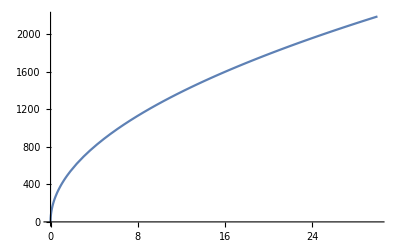

```mathematica
Plot[400 √t,{t,0,30}]
```

```mathematica
Solve[400 √t==2000,t]
```

{{t→25}}

```mathematica
2π Integrate[400 √t,t]
```

1600/3 π t^(3/2)

```mathematica
FourierTransform[Cos[1600/3 π t^(3/2)],t,f,FourierParameters->{0, -2*Pi}]
```

1/(19200 (5 π)^(2/3) Abs[f]^3)(Abs[f]^3 (3 π (-ⅈ √3 f π^(1/3) AiryAi[-(f^2 (π/5)^(2/3))/1600]+40 √3 5^(1/3) AiryAiPrime[-(f^2 (π/5)^(2/3))/1600]+ⅈ f π^(1/3) AiryBi[-(f^2 (π/5)^(2/3))/1600]+40 5^(1/3) AiryBiPrime[-(f^2 (π/5)^(2/3))/1600]) Cos[(π Abs[f]^3)/480000]-40 3^(2/3) 5^(1/3) Gamma[-1/3] HypergeometricPFQ[{5/12,11/12},{1/3,1/2,5/6},-(f^6 π^2)/230400000000]-2 ⅈ f (3 π)^(1/3) Gamma[-2/3] HypergeometricPFQ[{7/12,13/12},{1/2,2/3,7/6},-(f^6 π^2)/230400000000])+3 f^3 π (√3 f π^(1/3) AiryAi[-(f^2 (π/5)^(2/3))/1600]+40 ⅈ √3 5^(1/3) AiryAiPrime[-(f^2 (π/5)^(2/3))/1600]+f π^(1/3) AiryBi[-(f^2 (π/5)^(2/3))/1600]-40 ⅈ 5^(1/3) AiryBiPrime[-(f^2 (π/5)^(2/3))/1600]) Sin[(π Abs[f]^3)/480000])

```mathematica
r=%59;
```

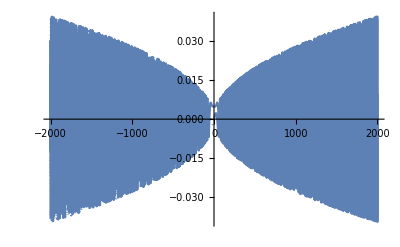

```mathematica
ReImPlot[r,{f,-2000,2000}]
```

```mathematica
AudioGenerator[Cos[1600/3 π t^(3/2)]/.t->#&,25]
```